```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(*reflectivities*)
Id = IdentityMatrix[2];
RBS= TBS =  1/2^(1/2)Id;
```

```mathematica
(*input quadratures*)
{nvec, avec, Avec} = {{{Subscript[n̂, 1]}, {Subscript[n̂, 2]}},{{Subscript[â, 1]}, {Subscript[â, 2]}},{{A Cos[θ]}, {A Sin[θ]}}};
lvec = Avec + avec;
(*dropping all spaces, no propagation*)
(*squeezer*)
SSqz[r_,ϕ_]:=({{Cos[2 ϕ]Sinh[r]+Cosh[r], Sin[2 ϕ]Sinh[r]}, {Sin[2 ϕ]Sinh[r], -Cos[2 ϕ]Sinh[r]+Cosh[r]}})
sqzvec = SSqz[r,ϕ].nvec;
```

```mathematica
(*frequency domain quadratures at the photodiodes*)
pd1vec = Simplify[TBS.lvec+RBS.sqzvec]
pd2vec = Simplify[TBS.sqzvec-RBS.lvec]
```

{{(A Cos[θ]+(â)_1+(Cosh[r]+Cos[2 ϕ] Sinh[r]) (n̂)_1+Sin[2 ϕ] Sinh[r] (n̂)_2)/(√2)},{(A Sin[θ]+(â)_2+Sin[2 ϕ] Sinh[r] (n̂)_1+Cosh[r] (n̂)_2-Cos[2 ϕ] Sinh[r] (n̂)_2)/(√2)}}

{{(-A Cos[θ]-(â)_1+(Cosh[r]+Cos[2 ϕ] Sinh[r]) (n̂)_1+Sin[2 ϕ] Sinh[r] (n̂)_2)/(√2)},{-(A Sin[θ]+(â)_2-Sin[2 ϕ] Sinh[r] (n̂)_1-Cosh[r] (n̂)_2+Cos[2 ϕ] Sinh[r] (n̂)_2)/(√2)}}

```mathematica
(*spotting frequency dependent parts by eye, using reasoning in sqz cavity notebook*)
({{Subscript[B, 1,c], Subscript[b̂, 1,c]}, {Subscript[B, 1,s], Subscript[b̂, 1,s]}, {Subscript[B, 2,c], Subscript[b̂, 2,c]}, {Subscript[B, 2,s], Subscript[b̂, 2,s]}})=({{A/2^(1/2) Cos[θ], pd1vec[[1]][[1]]-Subscript[B, 1,c]}, {A/2^(1/2) Sin[θ], pd1vec[[2]][[1]]-Subscript[B, 1,s]}, {-A/2^(1/2) Cos[θ], pd2vec[[1]][[1]]-Subscript[B, 2,c]}, {-A/2^(1/2) Sin[θ], pd2vec[[2]][[1]]-Subscript[B, 2,s]}});
(*homodyne intensity
if everything works, this should be indep of Subscript[â, i]*)
OverHat[HomI]=Simplify[Subscript[B, 1,c] Subscript[b̂, 1,c]+Subscript[B, 1,s] Subscript[b̂, 1,s]-Subscript[B, 2,c] Subscript[b̂, 2,c]-Subscript[B, 2,s] Subscript[b̂, 2,s]]
```

A ((Cos[θ] Cosh[r]+Cos[θ-2 ϕ] Sinh[r]) (n̂)_1+(Cosh[r] Sin[θ]-Sin[θ-2 ϕ] Sinh[r]) (n̂)_2)

```mathematica
(*co-efficients of n1 and n2*)
g1[r_,ϕ_,θ_]:=Cos[θ] Cosh[r]+Cos[θ-2 ϕ] Sinh[r]
g2[r_,ϕ_,θ_]:=Cosh[r] Sin[θ]-Sin[θ-2 ϕ] Sinh[r]
(*PSD of homodyne intensity
by reasoning in sqz cavity notebook, particularly
OverHat[Subscript[S, HomI]][Ω] 2π δ[Ω-Ω'] = ⟨0|OverHat[HomI][Ω]○OverHat[HomI]†[Ω']|0⟩
⟨0|Subscript[n̂, i][Ω]○Subscript[n̂, i][Ω']|0⟩ = 1/2 2πδ[Ω-Ω']*)
(*also setting A = 1*)
SHomI[r_,ϕ_,θ_]:= 1/2(g1[r,ϕ,θ]^2+g2[r,ϕ,θ]^2)
```

```mathematica
(*Plot[SHomI[r,0,0],{r,-1,1},
AxesLabel->{"squeezer parameter, r","PSD of homodyne intensity"},PlotLabel->"PSD of QHD against squeezer parameter\nfor simple squeezer configuration"]*)
```

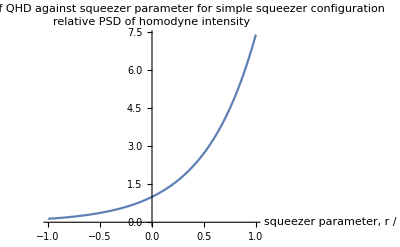

```mathematica
plot1 = Plot[SHomI[r,0,0]/SHomI[0,0,0],{r,-1,1},
AxesLabel->{"squeezer parameter, r\n/ (not in dB)","relative PSD of homodyne intensity"},PlotLabel->"relative PSD of QHD against squeezer parameter\n for simple squeezer configuration"]
Export["simple_squeezer_analytics_relative_PSD_vs_r.pdf",plot1];
```

```mathematica
sqzParamToGain[r_]:=10*Log10[Exp[r]]
gainToSqzParam[gain_]:=Log[10^(gain/10)]
```

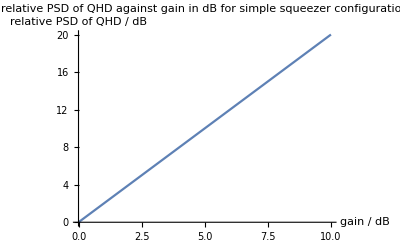

```mathematica
plot2 = Plot[10 Log10[SHomI[gainToSqzParam[gaindB],0,0]/SHomI[0,0,0]],{gaindB,0,10},
AxesLabel->{"gain / dB","relative PSD of QHD / dB"},PlotLabel->"relative PSD of QHD against gain in dB\nfor simple squeezer configuration"]
Export["simple_squeezer_analytics_relative_PSD_vs_gain_dB.pdf",plot2];
```

```mathematica
(*notebook needs to be saved for this to function*)
NotebookPrint[EvaluationNotebook[],NotebookDirectory[]<>"simple_squeezer_notebook.pdf"]
```